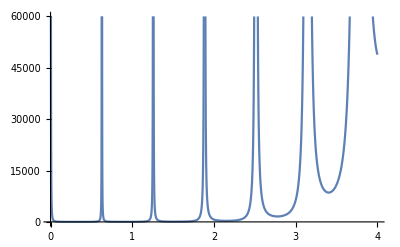

```mathematica
(*Question 1*)
gam=3;w=5;
Plot[1/NT(√(1-Exp[-2*NT*gam]*Cos[NT*w]^2))/(Exp[-NT*gam]*Sin[NT*w]^2),{NT,0,4}]
```

```mathematica
Clear["Global`*"]
Solve[D[,NT]==0]
```

$Aborted

```mathematica
FullSimplify[√(1-Exp[-2*NT*gam]*Cos[NT*w]^2)]
```

√(1-ⅇ^(-2 gam NT) Cos[NT w]^2)

```mathematica
TrigReduce[√(1-ⅇ^(-2 gam NT) Cos[NT w]^2)]
```

√(ⅇ^(-2 gam NT) (ⅇ^(2 gam NT)-Cos[NT w]^2))

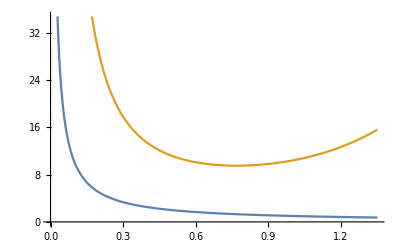

```mathematica
gam=2;
w=1;
Plot[{1/NT,(√(1-Exp[-2*NT*gam]*Cos[NT*w]^2))/(Exp[-NT*gam]*Sin[NT*w]^2)},{NT,0,2.7/2}]
```

```mathematica
Clear["Global`*"]
Solve[{D[(√(1-Exp[-2*NT*gam]*Cos[NT*w]^2))/(Exp[-NT*gam]*Sin[NT*w]^2),NT]==0,NT<3},NT]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{ⅇ^(gam NT) gam √(1-ⅇ^(-2 gam NT) Cos[NT w]^2) Csc[NT w]^2-2 ⅇ^(gam NT) w √(1-ⅇ^(-2 gam NT) Cos[NT w]^2) Cot[NT w] Csc[NT w]^2+(ⅇ^(gam NT) Csc[NT w]^2 (2 ⅇ^(-2 gam NT) gam Cos[NT w]^2+2 ⅇ^(-2 gam NT) w Cos[NT w] Sin[NT w]))/(2 √(1-ⅇ^(-2 gam NT) Cos[NT w]^2))==0,NT<3},NT]

```mathematica
FullSimplify[Solve[D[(√(1-Exp[-2n*T*gam]))/(n*w*T*Exp[-n*T*gam]),T]==0,T]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→(2+ProductLog[-2/ⅇ^2])/(2 gam n)}}

```mathematica
N[ProductLog[-2/E^2]]
```

-0.406376

```mathematica
FullSimplify[1/(n*T)*(√(1-Exp[-2*n*T*gam]*Cos[n*T*w]^2))/(Exp[-n*T*gam]*Sin[n*T*w]^2)/.T->1/(gam*n)]
```

gam √(ⅇ^2-Cos[w/gam]^2) Csc[w/gam]^2

```mathematica
TrigReduce[gam √(ⅇ^2-1^2) /(w/gam)^2]
```

(√(-1+ⅇ^2) gam^3)/w^2

```mathematica
(*Question 2*)
Integrate[S0*Exp[I*w*tc],{w,-1/tc,1/tc}]
```

(2 S0 Sin[1])/tc

```mathematica
Integrate[Cos[w*tc],{w,-1/tc,1/tc}]
```

(2 Sin[1])/tc

```mathematica
(*Question 3*)
FullSimplify[Cos[π*v*t+phi0]-Cos[phi0]]
```

-Cos[phi0]+Cos[phi0+π t v]

```mathematica
FullSimplify[1/2(I-I*Exp[-2I*(phi1-phi2)])1/2(-I+I*Exp[2I*(phi1-phi2)])]
```

Sin[phi1-phi2]^2

```mathematica
FullSimplify[1/(√2){{1,-I},{-I,1}}*1/(√2){{1,-I},{-I,1}}].{1,0}
```

{1/2,-1/2}

```mathematica
phi1=(gamma*B)/(4*π*v)(Cos[π*v*tau+phi0]-Cos[phi0])
phi2=(gamma*B)/(4*π*v)(Cos[2*π*v*tau+phi0]-Cos[π*v*tau+phi0])
```

(B gamma (-Cos[phi0]+Cos[phi0+π tau v]))/(4 π v)

(B gamma (-Cos[phi0+π tau v]+Cos[phi0+2 π tau v]))/(4 π v)

```mathematica
FullSimplify[Sin[phi1-phi2]^2]
```

Sin[(B gamma Cos[phi0+π tau v] Sin[(π tau v)/2]^2)/(π v)]^2

```mathematica
P=1/16 gamma^2 B^2 π^2 v^2 tau^4*Cos[π*v*tau+phi0]^2
dP=√(P(1-P))
dPdB=D[P,B]
FullSimplify[dP/dPdB]
```

1/16 B^2 gamma^2 π^2 tau^4 v^2 Cos[phi0+π tau v]^2

1/4 π √(B^2 gamma^2 tau^4 v^2 Cos[phi0+π tau v]^2 (1-1/16 B^2 gamma^2 π^2 tau^4 v^2 Cos[phi0+π tau v]^2))

1/8 B gamma^2 π^2 tau^4 v^2 Cos[phi0+π tau v]^2

1/(B gamma^2 π tau^4 v^2)2 √(B^2 gamma^2 tau^4 v^2 Cos[phi0+π tau v]^2-1/16 B^4 gamma^4 π^2 tau^8 v^4 Cos[phi0+π tau v]^4) Sec[phi0+π tau v]^2